```mathematica
V[l_,μ_,r_]:=-1/r+l^2/(μ r^2)
```

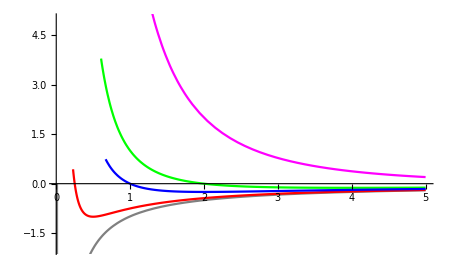

```mathematica
Table[{Show[
Plot[V[0.1,1,r],{r,0.01,5},PlotStyle->Gray],
Plot[V[0.5,1,r],{r,0.01,5},PlotStyle->Red],
Plot[V[1,0.1,r],{r,0.01,5},PlotStyle->Magenta],
Plot[V[1,0.5,r],{r,0.01,5},PlotStyle->Green],
Plot[V[1,1,r],{r,0.01,5},PlotStyle->Blue],PlotRange->{-2,5}],
SwatchLegend[{Gray,Red,Magenta,Green,Blue},{"l=0.1, μ=1","l=0.5, μ=1","l=1, μ=0.1","l=1, μ=0.5","l=1, μ=1"},LegendLabel->Placed["Legenda",Above]]}]
```

```mathematica
Ve[k_,μe_,r_]:=k/r+1/(μe r^2)
```

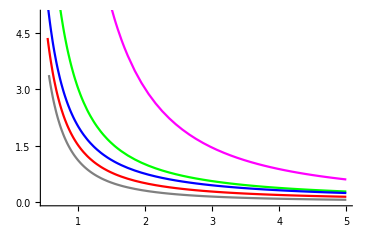

```mathematica
Table[{Show[
Plot[Ve[0.1,1,r],{r,0.01,5},PlotStyle->Gray],
Plot[Ve[0.5,1,r],{r,0.01,5},PlotStyle->Red],
Plot[Ve[1,0.1,r],{r,0.01,5},PlotStyle->Magenta],
Plot[Ve[1,0.5,r],{r,0.01,5},PlotStyle->Green],
Plot[Ve[1,1,r],{r,0.01,5},PlotStyle->Blue],PlotRange->{0,5}],
SwatchLegend[{Gray,Red,Magenta,Green,Blue},{"k=0.1, μe=1","k=0.5, μe=1","k=1, μe=0.1","k=1, μe=0.5","k=1, μe=1"},LegendLabel->Placed["Legenda",Above]]}]
```

```mathematica
Vef[m_,l_,r_]:=-m/r+l^2/(m^3 r^2)-(4 l^2)/(m^3 r^3)
```

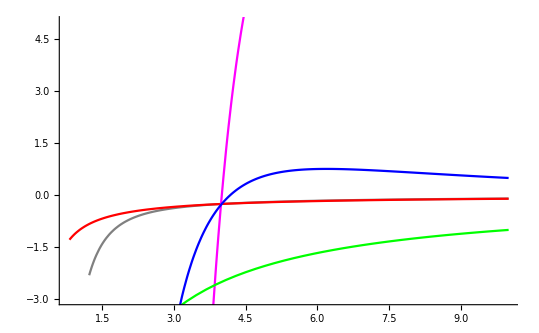

```mathematica
Table[{Show[
Plot[Vef[1,1,r],{r,0.01,10},PlotStyle->Gray],
Plot[Vef[1,0.1,r],{r,0.01,10},PlotStyle->Red],
Plot[Vef[0.1,1,r],{r,0.01,10},PlotStyle->Magenta],
Plot[Vef[10,1,r],{r,0.01,10},PlotStyle->Green],
Plot[Vef[1,10,r],{r,0.01,10},PlotStyle->Blue],PlotRange->{-3,5}],
SwatchLegend[{Gray,Red,Magenta,Green,Blue},{"m=1, l=1","m=1, l=0.1","m=0.1, l=1","m=10, l=1","m=1, l=10"},LegendLabel->Placed["Legenda",Above]]}]
```

```mathematica
FullSimplify[{(-m m)/r+l^2/(m r^2)-(4m l^2)/(m r^3)}/.{r->rd m}]
```

{(l^2 (-4+rd))/(m^3 rd^3)-m/rd}